## Calculation

```mathematica
wp=50;(* Working precision *)
ag=50;(* Accuracy goal *)
pg=50;(* Precision goal *)
q = Sqrt[2];
phiDEQ = ((-k^2 (-1+u) (-1+u (-1+q^2 u))+w^2) phi[u])/(4 (-1+u)^2 u (1+u-q^2 u^2)^2)+((-1+u (-1+q^2 u)) (-1+u^2 (-1+q^2 (-1+2 u))) phi'[u])/((-1+u) u (1+u-q^2 u^2)^2)+((-1+u (-1+q^2 u))^2 phi''[u])/((1+u-q^2 u^2)^2);
```

Extremal horizon expansion

```mathematica
order=40;
coefficients =Get["/home/finn/Documents/studienprojekt/ruleExt40"];
phiSeries[u_]:=  E^(-I w/(6 ( 1- u))) * (1-u)^(7 I w/36)* Sum[h[nn] (1-u)^nn, {nn, 0, order}];
horizonExpansion[u_] :=phiSeries[u] /. coefficients /. {h[0]->1, h[order]->0}
```

```mathematica
Table[ SetPrecision[ E^(-I w/(6 ( 1- u))) * (1-u)^(7 I w/36)* Sum[h[nn] (1-u)^nn, {nn, 0, i}]/.coefficients/.{h[0]->c0,h[order]->0}/.{c0->1, u->0.997, w->1/10, k->1/10},wp],{i,1,40}]
```

{0.81513322931079712496682532218983396887779235839844+0.5753806403371247712996705558907706290483474731445 ⅈ,0.81525479772885955931371881888480857014656066894531+0.5752186638548181241148427034204360097646713256836 ⅈ,0.81528361471112464897714744438417255878448486328125+0.5752409883761041564653737623302731662988662719727 ⅈ,0.81527750263497078542229701270116493105888366699219+0.5752487031099789982491188311541918665170669555664 ⅈ,0.81527474402098676353745076994528062641620635986328+0.5752464792698156470507342419296037405729293823242 ⅈ,0.81527575335950486223879352110088802874088287353516+0.5752452448559521869242416869383305311203002929688 ⅈ,0.81527641673013218071019991839420981705188751220703+0.5752457938187107711058843051432631909847259521484 ⅈ,0.81527606875005032005532257244340144097805023193359+0.5752462099731808775615604645281564444303512573242 ⅈ,0.81527577025086472861659103728015907108783721923828+0.5752459580759303747754529467783868312835693359375 ⅈ,0.81527597526464745669727562926709651947021484375+0.5752457171172393746161333183408714830875396728516 ⅈ,0.81527619145136542844198856982984580099582672119141+0.5752459024232974282853092518053017556667327880859 ⅈ,0.8152760072825859793965719291009008884429931640625+0.575246115833927373905964941513957455754280090332 ⅈ,0.81527577741217382989447060026577673852443695068359+0.5752459162219482058375774613523390144109725952148 ⅈ,0.81527601172549180041926319972844794392585754394531+0.5752456479404751688022656708199065178632736206055 ⅈ,0.81527634897482470499596729496261104941368103027344+0.5752459440736732432242206414230167865753173828125 ⅈ,0.81527594806244130243300105576054193079471588134766+0.5752463983650152323789939146081451326608657836914 ⅈ,0.81527529523358610585859196362434886395931243896484+0.5752458195217707848101440504251513630151748657227 ⅈ,0.81527618306639815237701895966893061995506286621094+0.5752448226479524029386425354459788650274276733398 ⅈ,0.81527779499865404844172189768869429826736450195313+0.5752462643071792891547033832466695457696914672852 ⅈ,0.8152753243023891371876743505708873271942138671875+0.5752490158261099884029476925206836313009262084961 ⅈ,0.81527037995362705569135641781031154096126556396484+0.5752445592396476792274029321561101824045181274414 ⅈ,0.81527881969760995772844580642413347959518432617188+0.5752352295671748771965781088510993868112564086914 ⅈ,0.8152972637276914014137219055555760860443115234375+0.5752519719942592590911090155714191496372222900391 ⅈ,0.81526254409221288188547305253450758755207061767578+0.5752900940926727324509215577563736587762832641602 ⅈ,0.81518031878314967109133704070700332522392272949219+0.5752149697105635173244309044093824923038482666016 ⅈ,0.81534962926013465622787634856649674475193023681641+0.5750302192603894413380771766242105513811111450195 ⅈ,0.81578136670455270174073802991188131272792816162109+0.5754270368868444895937841465638484805822372436523 ⅈ,0.81481562375551563892628337271162308752536773681641+0.5764748016069213276679761293053161352872848510742 ⅈ,0.81217856252248699089335559619939886033535003662109+0.5740375441258535049726674515113700181245803833008 ⅈ,0.8185488349386549344899322022683918476104736328125+0.5671631635868925602750323378131724894046783447266 ⅈ,0.83708782459244668316955539921764284372329711914063+0.5843864566011327532635277748340740799903869628906 ⅈ,0.78897126431373687527326410418027080595493316650391+0.6360511562635543514332425729662645608186721801758 ⅈ,0.64034208610988929688545567842083983123302459716797+0.4972981862908495420683152588026132434606552124023 ⅈ,1.0529486965556895672335713243228383362293243408203+0.0563460625100491996342100264882901683449745178223 ⅈ,2.4008443603397098264906617259839549660682678222656+1.320437054804434628962894748838152736425399780273 ⅈ,-1.585674999350385805385599269357044249773025512695+5.56196238145208354808346484787762165069580078125 ⅈ,-15.314504520090022055001099943183362483978271484375-7.368945738977994430740636744303628802299499511719 ⅈ,27.7926511876249691113116568885743618011474609375-53.04144876888799586822642595507204532623291015625 ⅈ,183.8442016442219255623058415949344635009765625+94.542221986763166796663426794111728668212890625 ⅈ,183.8442016442219255623058415949344635009765625+94.542221986763166796663426794111728668212890625 ⅈ}

Solve DEQ

```mathematica
epsilon=1/1000000000; uBnum=epsilon;uHnum=1-1/1000;

Clear[solphi]
solphi[omega_?NumericQ,kay_,c0_]:=
Block[
{w=omega,k=kay},
	Print["Shear Mode for omega: ", omega, " k: ", kay];
	NDSolve[
	{0==phiDEQ,
	phi[uHnum]==horizonExpansion[uHnum],
		phi'[uHnum]==(D[horizonExpansion[u],u]/.{u->uHnum})
		},
		phi[u],{u,uBnum,uHnum},
		WorkingPrecision->wp,AccuracyGoal->ag,PrecisionGoal->pg,MaxSteps->100000
]
]

(* Usage: phiSol(w, k) *)
phiSol[w_?NumericQ, k_]:=SetPrecision[solphi[w,k,1][[1,1,2]],wp]
```

Shear Mode for omega: 2.-3.5 ⅈ k: 0

NDSolve::precw: The precision of the differential equation ({{0==-((2.0625+3.5 ⅈ) phi[u])/((-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==-4.1315×10^-256-5.4483×10^-257 ⅈ,phi'[999/1000]==2.23103×10^-250+1.69696×10^-250 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

-8.858335285695613888673883539056791584568980019858×10^-243+6.3956504596817365505192992039848292425938684183×10^-244 ⅈ

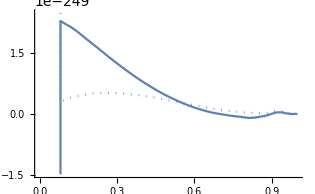

```mathematica
sol = phiSol[2.0 -3.5I, 0];
sol /. u->(uBnum) // Print;
ReImPlot[phi[u] /.{phi[u] -> sol}, {u, uBnum, uHnum}]
```

```mathematica
qnmRoutine[initWR_,initWI_,kay_,kuh_]:=Block[
{iWR=initWR,iWI=initWI,k=kay,q=kuh},
eqQNMVBC[wR_?NumericQ,wI_?NumericQ]:=SetPrecision[Block[{w=wR+ⅈ wI},phiSol[w,k]/.u->uBnum],wp];
findQNMVBC[reWi_?NumericQ,imWi_?NumericQ]:=
FindRoot[
{
Re[eqQNMVBC[wr,wi]]==0,
Im[eqQNMVBC[wr,wi]]==0},
{wr,reWi},{wi,imWi},
WorkingPrecision->wp,
AccuracyGoal->ag,
PrecisionGoal->pg
];
qnmVBC=SetPrecision[findQNMVBC[iWR,iWI],wp];
Print[{qnmVBC[[1,2]],qnmVBC[[2,2]]}]
]
```

```mathematica
qnmRoutine[4/100,-13/1000,1/2,Sqrt[2]]
```

Shear Mode for omega: 0.04-0.013 ⅈ k: 1/2

NDSolve::precw: The precision of the differential equation ({{0==(((0.001431-0.00104 ⅈ)-1/4 Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==0.103813758719148197824250846410789349799542436859-0.047701900952855995232815443356385300683471252767 ⅈ,phi'[999/1000]==-618.42945910798467449587329354341981519740691119-593.53121510601995861205768808107291230548561187 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at u == 0.999.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

Shear Mode for omega: 0.04-0.013 ⅈ k: 1/2

NDSolve::precw: The precision of the differential equation ({{0==(((0.001431-0.00104 ⅈ)-1/4 Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==0.103813758719148197824250846410789349799542436859-0.047701900952855995232815443356385300683471252767 ⅈ,phi'[999/1000]==-618.42945910798467449587329354341981519740691119-593.53121510601995861205768808107291230548561187 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at u == 0.999.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

Shear Mode for omega: 0.04-0.013 ⅈ k: 1/2

NDSolve::precw: The precision of the differential equation ({{0==(((0.001431-0.00104 ⅈ)-1/4 Plus[«2»] Plus[«2»]) phi[u])/(4 (-1+u)^2 u (1+u+Times[«2»])^2)+((-1+u Plus[«2»]) (-1+Power[«2»] Plus[«2»]) phi'[u])/((-1+u) u (1+u+Times[«2»])^2)+((-1+Times[«2»])^2 phi''[u])/(1+u+Times[«2»])^2,phi[999/1000]==0.103813758719148197824250846410789349799542436859-0.047701900952855995232815443356385300683471252767 ⅈ,phi'[999/1000]==-618.42945910798467449587329354341981519740691119-593.53121510601995861205768808107291230548561187 ⅈ},{},{},{},{}}) is less than WorkingPrecision (50.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

NDSolve::ndtol: Tolerances requested by the AccuracyGoal and PrecisionGoal options could not be achieved at u == 0.999.

General::stop: Further output of NDSolve::ndtol will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {1/1000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Shear Mode for omega: 0.040000000000000000000000100000000000000566341900943-0.013 ⅈ k: 1/2

Shear Mode for omega: 0.04-0.012999999999999999999999899999999999999433658099057 ⅈ k: 1/2

Shear Mode for omega: 0.039343229840436341495318728972370539967955023731246-0.018038067100373482470014852957527129870172393359769 ⅈ k: 1/2

Shear Mode for omega: 0.039343229840436341495318728972370539967955023731246-0.018038067100373482470014852957527129870172393359769 ⅈ k: 1/2

Shear Mode for omega: 0.039343229840436341495318828972370539968521365632188-0.018038067100373482470014852957527129870172393359769 ⅈ k: 1/2

Shear Mode for omega: 0.039343229840436341495318728972370539967955023731246-0.018038067100373482470014752957527129869606051458827 ⅈ k: 1/2

Shear Mode for omega: 0.037847268414796658653225185098211391357803953678968-0.024390566434793125399717538130068057096471666675437 ⅈ k: 1/2

Shear Mode for omega: 0.037847268414796658653225185098211391357803953678968-0.024390566434793125399717538130068057096471666675437 ⅈ k: 1/2

Shear Mode for omega: 0.037847268414796658653225285098211391358370295579911-0.024390566434793125399717538130068057096471666675437 ⅈ k: 1/2

Shear Mode for omega: 0.037847268414796658653225185098211391357803953678968-0.024390566434793125399717438130068057095905324774494 ⅈ k: 1/2

Shear Mode for omega: 0.036070591162364954217007172280577100071573610578609-0.03071426714715084268852905180349522493961194370351 ⅈ k: 1/2

Shear Mode for omega: 0.036070591162364954217007172280577100071573610578609-0.03071426714715084268852905180349522493961194370351 ⅈ k: 1/2

Shear Mode for omega: 0.036070591162364954217007272280577100072139952479552-0.03071426714715084268852905180349522493961194370351 ⅈ k: 1/2

Shear Mode for omega: 0.036070591162364954217007172280577100071573610578609-0.030714267147150842688528951803495224939045601802567 ⅈ k: 1/2

Shear Mode for omega: 0.03433367157005345195754556931790359459431782338324-0.037258096483414913356076908560904501195305236499919 ⅈ k: 1/2

Shear Mode for omega: 0.03433367157005345195754556931790359459431782338324-0.037258096483414913356076908560904501195305236499919 ⅈ k: 1/2

Shear Mode for omega: 0.034333671570053451957545669317903594594884165284183-0.037258096483414913356076908560904501195305236499919 ⅈ k: 1/2

Shear Mode for omega: 0.03433367157005345195754556931790359459431782338324-0.037258096483414913356076808560904501194738894598976 ⅈ k: 1/2

Shear Mode for omega: 0.032762715057712460596752203579847693414298813143912-0.044059601905553058488158090245928800011643926940609 ⅈ k: 1/2

Shear Mode for omega: 0.032762715057712460596752203579847693414298813143912-0.044059601905553058488158090245928800011643926940609 ⅈ k: 1/2

Shear Mode for omega: 0.032762715057712460596752303579847693414865155044855-0.044059601905553058488158090245928800011643926940609 ⅈ k: 1/2

Shear Mode for omega: 0.032762715057712460596752203579847693414298813143912-0.044059601905553058488157990245928800011077585039667 ⅈ k: 1/2

Shear Mode for omega: 0.031427019112637657299143257342088892984231094224414-0.051043267187874228779817493435135601489191198243853 ⅈ k: 1/2

Shear Mode for omega: 0.031427019112637657299143257342088892984231094224414-0.051043267187874228779817493435135601489191198243853 ⅈ k: 1/2

Shear Mode for omega: 0.031427019112637657299143357342088892984797436125357-0.051043267187874228779817493435135601489191198243853 ⅈ k: 1/2

Shear Mode for omega: 0.031427019112637657299143257342088892984231094224414-0.05104326718787422877981739343513560148862485634291 ⅈ k: 1/2

Shear Mode for omega: 0.030342397520560188925273582026448239081095594300347-0.058109026346155784623118803371651942711067303711465 ⅈ k: 1/2

Shear Mode for omega: 0.030342397520560188925273582026448239081095594300347-0.058109026346155784623118803371651942711067303711465 ⅈ k: 1/2

Shear Mode for omega: 0.030342397520560188925273682026448239081661936201289-0.058109026346155784623118803371651942711067303711465 ⅈ k: 1/2

Shear Mode for omega: 0.030342397520560188925273582026448239081095594300347-0.058109026346155784623118703371651942710500961810523 ⅈ k: 1/2

Shear Mode for omega: 0.029480212514218298716111759007843332835773550438456-0.06517928447256824639507414442778390139350765799929 ⅈ k: 1/2

Shear Mode for omega: 0.029480212514218298716111759007843332835773550438456-0.06517928447256824639507414442778390139350765799929 ⅈ k: 1/2

Shear Mode for omega: 0.029480212514218298716111859007843332836339892339399-0.06517928447256824639507414442778390139350765799929 ⅈ k: 1/2

Shear Mode for omega: 0.029480212514218298716111759007843332835773550438456-0.065179284472568246395074044427783901392941316098347 ⅈ k: 1/2

Shear Mode for omega: 0.028795847747439072424531493914332545476389159069629-0.072209824942587327348170164030391934351146045560875 ⅈ k: 1/2

Shear Mode for omega: 0.028795847747439072424531493914332545476389159069629-0.072209824942587327348170164030391934351146045560875 ⅈ k: 1/2

Shear Mode for omega: 0.028795847747439072424531593914332545476955500970572-0.072209824942587327348170164030391934351146045560875 ⅈ k: 1/2

Shear Mode for omega: 0.028795847747439072424531493914332545476389159069629-0.072209824942587327348170064030391934350579703659932 ⅈ k: 1/2

Shear Mode for omega: 0.028247395342872006634461724714945867320114268149238-0.079181437650132967430600292462110576684155299024041 ⅈ k: 1/2

Shear Mode for omega: 0.028247395342872006634461724714945867320114268149238-0.079181437650132967430600292462110576684155299024041 ⅈ k: 1/2

Shear Mode for omega: 0.028247395342872006634461824714945867320680610050181-0.079181437650132967430600292462110576684155299024041 ⅈ k: 1/2

Shear Mode for omega: 0.028247395342872006634461724714945867320114268149238-0.079181437650132967430600192462110576683588957123099 ⅈ k: 1/2

Shear Mode for omega: 0.027801616620871283500362473376601326145314703039298-0.086088986662871226290493299448528270631090708676071 ⅈ k: 1/2

Shear Mode for omega: 0.027801616620871283500362473376601326145314703039298-0.086088986662871226290493299448528270631090708676071 ⅈ k: 1/2

Shear Mode for omega: 0.027801616620871283500362573376601326145881044940241-0.086088986662871226290493299448528270631090708676071 ⅈ k: 1/2

Shear Mode for omega: 0.027801616620871283500362473376601326145314703039298-0.086088986662871226290493199448528270630524366775129 ⅈ k: 1/2

Shear Mode for omega: 0.027433783271063822256102755530342111831023597654401-0.092934060714205596283862065223956671848997860804662 ⅈ k: 1/2

NDSolve::mxst: Maximum number of 100000 steps reached at the point u == 0.99899984639090925990582017554598094298061868682218.

Shear Mode for omega: 0.027764833285890537375936501591975404713885592500809-0.08677349406800466328983017602607111075288142388893 ⅈ k: 1/2

NDSolve::mxst: Maximum number of 100000 steps reached at the point u == 0.99899986285982030853178590783217030372745615372294.

Shear Mode for omega: 0.027797938287373208887919876198138734002171791985449-0.086157437403384569990426987106282554643269780197357 ⅈ k: 1/2

Shear Mode for omega: 0.027797938287373208887919876198138734002171791985449-0.086157437403384569990426987106282554643269780197357 ⅈ k: 1/2

Shear Mode for omega: 0.027797938287373208887919976198138734002738133886392-0.086157437403384569990426987106282554643269780197357 ⅈ k: 1/2

Shear Mode for omega: 0.027797938287373208887919876198138734002171791985449-0.086157437403384569990426887106282554642703438296415 ⅈ k: 1/2

Shear Mode for omega: 0.027430777659062599245940728010078234446002591970918-0.093001905744408065281685359321051877827895800775076 ⅈ k: 1/2

NDSolve::mxst: Maximum number of 100000 steps reached at the point u == 0.99899984606881187252282959388294745674605196703757.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

Shear Mode for omega: 0.027761222224542147923721961379332684046554871983996-0.086841884237486919519552824327759486961732382255129 ⅈ k: 1/2

Shear Mode for omega: 0.027794266681090102791500084716258129006610099985304-0.086225882086794804943339570828430247875116040403134 ⅈ k: 1/2

Shear Mode for omega: 0.027794266681090102791500084716258129006610099985304-0.086225882086794804943339570828430247875116040403134 ⅈ k: 1/2

Shear Mode for omega: 0.027794266681090102791500184716258129007176441886247-0.086225882086794804943339570828430247875116040403134 ⅈ k: 1/2

Shear Mode for omega: 0.027794266681090102791500084716258129006610099985304-0.086225882086794804943339470828430247874549698502192 ⅈ k: 1/2

Shear Mode for omega: 0.027427777021963956281517999088769643755947669622961-0.093069745188256239590926598534300143627430769711451 ⅈ k: 1/2

Shear Mode for omega: 0.02775761771517748814050187615350928048154385694907-0.086910268396940948408098273599017237450347513333966 ⅈ k: 1/2

Shear Mode for omega: 0.027790601784498841326400263859983244154103475681681-0.086294320717809419289815441105488946832639187696218 ⅈ k: 1/2

Shear Mode for omega: 0.027790601784498841326400263859983244154103475681681-0.086294320717809419289815441105488946832639187696218 ⅈ k: 1/2

Shear Mode for omega: 0.027790601784498841326400363859983244154669817582623-0.086294320717809419289815441105488946832639187696218 ⅈ k: 1/2

Shear Mode for omega: 0.027790601784498841326400263859983244154103475681681-0.086294320717809419289815341105488946832072845795275 ⅈ k: 1/2

Shear Mode for omega: 0.027424781347782573993926479578382455050116054967316-0.093137579051693606802753248870185959241494866264208 ⅈ k: 1/2

$Aborted